```mathematica
NotebookEvaluate[NotebookDirectory[]<>"/split_step.nb"];
```

GPE solver v1.4, RZ 2019

```mathematica
HarmonicTrap2D[0.01,1.0];
sizes={256,64};
timeStep=0.001;
k=0.3;
contactInteractionFactor=4 Pi k;
initialize[];
gridReport
```

sizes | dim | len | max | min | delta | deltak | maxk
{256,64} | 2 | 16384 | {50.,5.} | {-50.,-5.} | {0.392157,0.15873} | {0.0625864,0.618501} | {8.01106,19.792}

```mathematica
calcAllTable
p1x=ListPlot[projectionX,Joined->True,PlotRange->All];
p1y=ListPlot[projectionY,Joined->True,PlotRange->All];
```

time | energies | moments | misc
(0) | (total | 0.535
kinetic | 0.2525
potential | 0.2525
contact | 0.03
virial | 0.06) | (meanX | 0
meanY | 0
sigmaX | 7.07107
sigmaY | 0.707107
norm | 1.) | (steps | 0
A0 | 0.178405)

```mathematica
AbsoluteTiming[evolve["ite",100,20]]
```

{243.562,Null}

time | energies | moments | misc
(100.) | (total | 0.524916
kinetic | 0.24691
potential | 0.262206
contact | 0.0158
virial | 0.00100897) | (meanX | 0
meanY | 0
sigmaX | 12.7227
sigmaY | 0.712899
norm | 1.) | (steps | 100000
A0 | 0.122751)

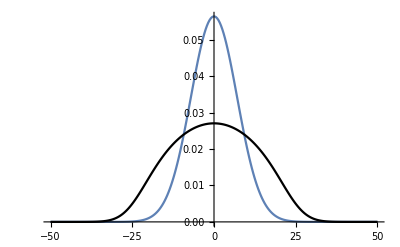

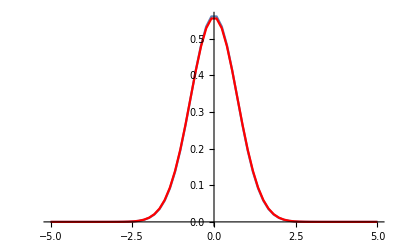

```mathematica
calcAllTable
p2x=ListPlot[projectionX,Joined->True,PlotRange->All,PlotStyle->Black];
p2y=ListPlot[projectionY,Joined->True,PlotRange->All,PlotStyle->Red];
Show[p1x,p2x,PlotRange->All]
Show[p1y,p2y,PlotRange->All]
```

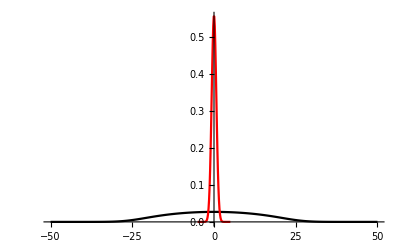

```mathematica
Show[p2x,p2y,PlotRange->{{-50,50},All}]
```

```mathematica
reportEnergies
```

time | total | kinetic | potential | contact | virial
0 | 0.535 | 0.2525 | 0.2525 | 0.03 | 0.06
5. | 0.530962 | 0.245578 | 0.259839 | 0.0255454 | 0.0225674
10. | 0.528961 | 0.245908 | 0.259832 | 0.0232213 | 0.0185928
15. | 0.527746 | 0.246142 | 0.259958 | 0.021646 | 0.0156584
20. | 0.52695 | 0.246312 | 0.260139 | 0.0204987 | 0.0133441
25. | 0.526404 | 0.24644 | 0.26034 | 0.0196234 | 0.0114479
30. | 0.526017 | 0.246538 | 0.260544 | 0.0189343 | 0.00985777
35. | 0.525736 | 0.246615 | 0.260742 | 0.0183793 | 0.00850431
40. | 0.525529 | 0.246675 | 0.260929 | 0.017925 | 0.0073411
45. | 0.525375 | 0.246723 | 0.261104 | 0.0175486 | 0.00633501
50. | 0.525259 | 0.246761 | 0.261264 | 0.0172337 | 0.00546118
55. | 0.525171 | 0.246792 | 0.261411 | 0.0169686 | 0.00470017
60. | 0.525105 | 0.246817 | 0.261543 | 0.0167441 | 0.00403632
65. | 0.525054 | 0.246838 | 0.261663 | 0.0165533 | 0.00345668
70. | 0.525016 | 0.246855 | 0.26177 | 0.0163904 | 0.00295035
75. | 0.524986 | 0.246869 | 0.261866 | 0.0162511 | 0.00250803
80. | 0.524964 | 0.246881 | 0.261952 | 0.0161317 | 0.00212167
85. | 0.524947 | 0.24689 | 0.262027 | 0.0160292 | 0.00178431
90. | 0.524934 | 0.246898 | 0.262094 | 0.0159411 | 0.00148986
95. | 0.524924 | 0.246905 | 0.262154 | 0.0158653 | 0.00123297
100. | 0.524916 | 0.24691 | 0.262206 | 0.0158 | 0.00100897

```mathematica
reportMoments
```

time | meanX | meanY | sigmaX | sigmaY | norm
0 | 0 | 0 | 7.07107 | 0.707107 | 1.
5. | 0 | 0 | 7.98657 | 0.71645 | 1.
10. | 0 | 0 | 8.71297 | 0.715593 | 1.
15. | 0 | 0 | 9.31046 | 0.715016 | 1.
20. | 0 | 0 | 9.81218 | 0.714598 | 1.
25. | 0 | 0 | 10.2392 | 0.71428 | 1.
30. | 0 | 0 | 10.606 | 0.71403 | 1.
35. | 0 | 0 | 10.9232 | 0.713829 | 1.
40. | 0 | 0 | 11.1985 | 0.713665 | 1.
45. | 0 | 0 | 11.4384 | 0.713529 | 1.
50. | 0 | 0 | 11.6477 | 0.713415 | 1.
55. | 0 | 0 | 11.8306 | 0.71332 | 1.
60. | 0 | 0 | 11.9905 | 0.713239 | 1.
65. | 0 | 0 | 12.1304 | 0.71317 | 1.
70. | 0 | 0 | 12.2527 | 0.713111 | 1.
75. | 0 | 0 | 12.3597 | 0.713061 | 1.
80. | 0 | 0 | 12.4532 | 0.713018 | 1.
85. | 0 | 0 | 12.5349 | 0.712981 | 1.
90. | 0 | 0 | 12.6062 | 0.71295 | 1.
95. | 0 | 0 | 12.6684 | 0.712922 | 1.
100. | 0 | 0 | 12.7227 | 0.712899 | 1.

```mathematica
wf0=wf;
psi0=psi;
```

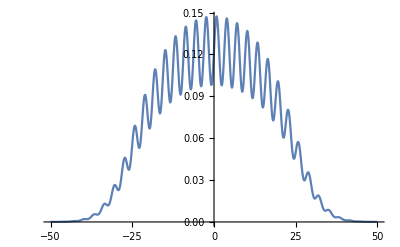

```mathematica
fnc[{x_,y_}]:=(psi0 @@{x,y})(1+0.2Sin[2x]);
Plot[Abs[fnc[{x,0}]],{x,-50,50},PlotRange->All]
wf=Map[fnc,mesh[],{dim}];
```

```mathematica
plot:=AppendTo[lplots,{time,ListPlot[projectionX,Joined->True,PlotRange->All,PlotStyle->Black,Filling->0],ListPlot[projectionY,Joined->True,PlotRange->All,PlotStyle->Red],psi}];
reset[];
newPotential[free];
k=-2;
contactInteractionFactor=4 Pi k;
AbsoluteTiming[evolve["rte",250,50,50]]
```

{825.565,Null}

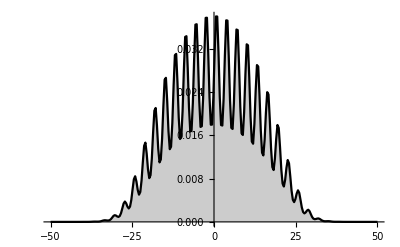
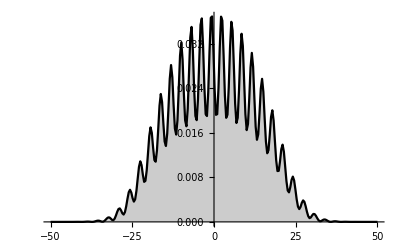
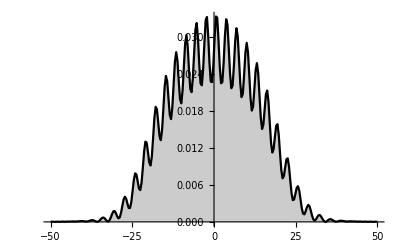
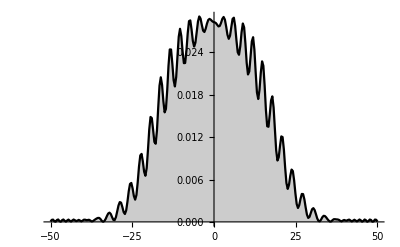
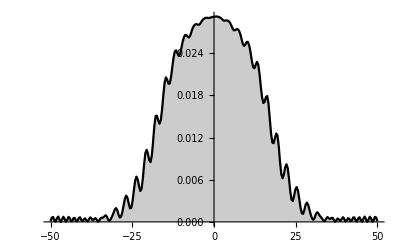
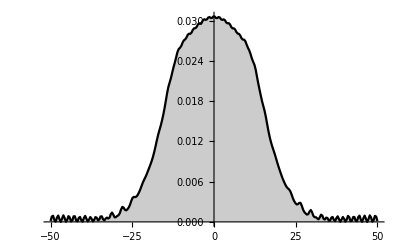
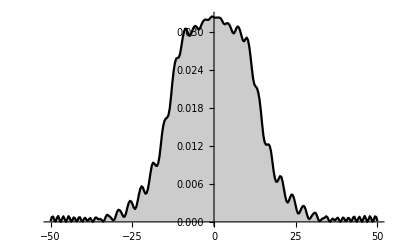
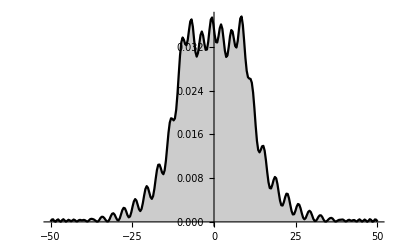

```mathematica
Map[Show[#,PlotRange->{{-50,50},All}]&,lplots[[All,2]]]
```